```mathematica
(* Filename: Time_By_w2_revA_SRCK2_avr_Al_DN
*)
(* Ver. 0 (28-Aug-2025) *)
(*
This file is used to prepare for a plot in Fig. 2.
*)
```

```mathematica
nn=127;
```

```mathematica
(***** In the following line, you need to set a path 
to the folder "For_figs_1_2". *****)
(*
datadir= "D:/.../For_figs_1_2/";
*)
```

```mathematica
mydirA80 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al_DN/dt=1_4/St80_Se16_Tr1000_B256"];
(***)
mydirA53 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al_DN/dt=1_8/St53_Se16_Tr1000_B256"];
(***)
mydirA38 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al_DN/dt=1_16/St38_Se16_Tr1000_B256"];
(***)
mydirA28 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al_DN/dt=1_32/St28_Se16_Tr1000_B256"];
(***)
mydirA19 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al_DN/dt=1_64/St19_Se16_Tr1000_B256"];
(***)
mydirA14 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al_DN/dt=1_128/St14_Se16_Tr1000_B256"];
```

```mathematica
numSetForTime=16;(* 16, 1 *)
```

```mathematica
tmpfname=StringJoin["/Set_",ToString[1],"/timefile"];
tmpMiniList=Import[mydirA80<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListA80={locTmp};
For[iiset = 2,iiset≤numSetForTime,iiset++,
tmpfname=StringJoin["/Set_",ToString[iiset],"/timefile"];
tmpMiniList=Import[mydirA80<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListA80=Append[timeListA80,locTmp];
];
(***)
tmpfname=StringJoin["/Set_",ToString[1],"/timefile"];
tmpMiniList=Import[mydirA53<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListA53={locTmp};
For[iiset = 2,iiset≤numSetForTime,iiset++,
tmpfname=StringJoin["/Set_",ToString[iiset],"/timefile"];
tmpMiniList=Import[mydirA53<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListA53=Append[timeListA53,locTmp];
];
(***)
tmpfname=StringJoin["/Set_",ToString[1],"/timefile"];
tmpMiniList=Import[mydirA38<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListA38={locTmp};
For[iiset = 2,iiset≤numSetForTime,iiset++,
tmpfname=StringJoin["/Set_",ToString[iiset],"/timefile"];
tmpMiniList=Import[mydirA38<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListA38=Append[timeListA38,locTmp];
];
(***)
tmpfname=StringJoin["/Set_",ToString[1],"/timefile"];
tmpMiniList=Import[mydirA28<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListA28={locTmp};
For[iiset = 2,iiset≤numSetForTime,iiset++,
tmpfname=StringJoin["/Set_",ToString[iiset],"/timefile"];
tmpMiniList=Import[mydirA28<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListA28=Append[timeListA28,locTmp];
];
(***)
tmpfname=StringJoin["/Set_",ToString[1],"/timefile"];
tmpMiniList=Import[mydirA19<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListA19={locTmp};
For[iiset = 2,iiset≤numSetForTime,iiset++,
tmpfname=StringJoin["/Set_",ToString[iiset],"/timefile"];
tmpMiniList=Import[mydirA19<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListA19=Append[timeListA19,locTmp];
];
```

```mathematica
numSubSetForTime=8;(* 1, 2, 4, 8, 16 *)
numMiniSet=numSetForTime/numSubSetForTime;
```

```mathematica
timeListA80SubSum=Table[{},{iiset,1,numSubSetForTime}];
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForTime,ll++,
timeListA80SubSum[[ll]]=timeListA80[[tmpSt,2]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
timeListA80SubSum[[ll]]+=timeListA80[[iiset,2]];
];
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
(***)
timeListA53SubSum=Table[{},{iiset,1,numSubSetForTime}];
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForTime,ll++,
timeListA53SubSum[[ll]]=timeListA53[[tmpSt,2]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
timeListA53SubSum[[ll]]+=timeListA53[[iiset,2]];
];
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
(***)
timeListA38SubSum=Table[{},{iiset,1,numSubSetForTime}];
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForTime,ll++,
timeListA38SubSum[[ll]]=timeListA38[[tmpSt,2]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
timeListA38SubSum[[ll]]+=timeListA38[[iiset,2]];
];
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
(***)
timeListA28SubSum=Table[{},{iiset,1,numSubSetForTime}];
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForTime,ll++,
timeListA28SubSum[[ll]]=timeListA28[[tmpSt,2]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
timeListA28SubSum[[ll]]+=timeListA28[[iiset,2]];
];
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
(***)
timeListA19SubSum=Table[{},{iiset,1,numSubSetForTime}];
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForTime,ll++,
timeListA19SubSum[[ll]]=timeListA19[[tmpSt,2]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
timeListA19SubSum[[ll]]+=timeListA19[[iiset,2]];
];
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
```

```mathematica
timeA80Ave=Mean[timeListA80SubSum];
timeA80Std=Sqrt[Total[(timeListA80SubSum-timeA80Ave)^2]/numSubSetForTime];
(***)
timeA53Ave=Mean[timeListA53SubSum];
timeA53Std=Sqrt[Total[(timeListA53SubSum-timeA53Ave)^2]/numSubSetForTime];
(***)
timeA38Ave=Mean[timeListA38SubSum];
timeA38Std=Sqrt[Total[(timeListA38SubSum-timeA38Ave)^2]/numSubSetForTime];
(***)
timeA28Ave=Mean[timeListA28SubSum];
timeA28Std=Sqrt[Total[(timeListA28SubSum-timeA28Ave)^2]/numSubSetForTime];
(***)
timeA19Ave=Mean[timeListA19SubSum];
timeA19Std=Sqrt[Total[(timeListA19SubSum-timeA19Ave)^2]/numSubSetForTime];
```

```mathematica
tmpMini=Table[{},{ii,1,5}];
tmpMini[[1]]={Log[2,timeA80Ave],Log[2,1/4]};
tmpMini[[2]]={Log[2,timeA53Ave],Log[2,1/8]};
tmpMini[[3]]={Log[2,timeA38Ave],Log[2,1/16]};
tmpMini[[4]]={Log[2,timeA28Ave],Log[2,1/32]};
tmpMini[[5]]={Log[2,timeA19Ave],Log[2,1/64]};
listTimeAForAve=Table[tmpMini[[ii]],{ii,1,5}];
```

```mathematica
plotlistTimeAForAve=ListPlot[listTimeAForAve];
```

```mathematica
tmpStep=1/4;
plotMiniBarA80ForTime=ListPlot[{{Log[2,timeA80Ave+timeA80Std],Log[2,tmpStep]},{Log[2,timeA80Ave-timeA80Std],Log[2,tmpStep]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarA53ForTime=ListPlot[{{Log[2,timeA53Ave+timeA53Std],Log[2,tmpStep]},{Log[2,timeA53Ave-timeA53Std],Log[2,tmpStep]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarA38ForTime=ListPlot[{{Log[2,timeA38Ave+timeA38Std],Log[2,tmpStep]},{Log[2,timeA38Ave-timeA38Std],Log[2,tmpStep]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarA28ForTime=ListPlot[{{Log[2,timeA28Ave+timeA28Std],Log[2,tmpStep]},{Log[2,timeA28Ave-timeA28Std],Log[2,tmpStep]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarA19ForTime=ListPlot[{{Log[2,timeA19Ave+timeA19Std],Log[2,tmpStep]},{Log[2,timeA19Ave-timeA19Std],Log[2,tmpStep]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
```

```mathematica
tmpUpperListA={{Log[2,timeA80Ave+timeA80Std],Log[2,1/4]},{Log[2,timeA53Ave+timeA53Std],Log[2,1/8]},{Log[2,timeA38Ave+timeA38Std],Log[2,1/16]},{Log[2,timeA28Ave+timeA28Std],Log[2,1/32]},{Log[2,timeA19Ave+timeA19Std],Log[2,1/64]}};
tmpLowerListA={{Log[2,timeA80Ave-timeA80Std],Log[2,1/4]},{Log[2,timeA53Ave-timeA53Std],Log[2,1/8]},{Log[2,timeA38Ave-timeA38Std],Log[2,1/16]},{Log[2,timeA28Ave-timeA28Std],Log[2,1/32]},{Log[2,timeA19Ave-timeA19Std],Log[2,1/64]}};
```

```mathematica
tmpLine=Line[{{0.,0.},{0,0.5}}];
tmpSize=5.0; (* 5.0, 10.0 *)
Graphics[{Gray(*RGBColor[0,0,1]*),tmpLine},AspectRatio->NCache[GoldenRatio^(-1),0.6180339887498948],Axes->None,AxesOrigin->{0,0},ImageSize->{tmpSize,Automatic},Method->{},PlotRange->{{0,0},{0,0.5}},PlotRangeClipping->True,PlotRangePadding->{{0.,0.},{0.01,0.01}}]
```

-Graphics-

```mathematica
plotMarkerListAForTime=ListPlot[{tmpLowerListA,tmpUpperListA},PlotMarkers->{"",""}(*,PlotMarkers->{"",""}*)];
```

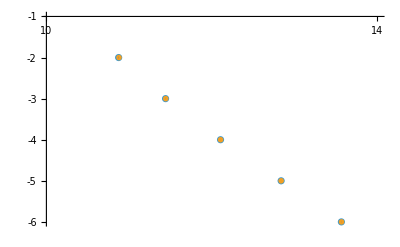

```mathematica
ll=0.015;
Show[plotlistTimeAForAve,plotMarkerListAForTime,plotMiniBarA80ForTime,plotMiniBarA53ForTime,plotMiniBarA38ForTime,plotMiniBarA28ForTime,plotMiniBarA19ForTime,PlotRange->{{10+0.05,14}(*{10.85,10.9}*),{-6,-1}},AxesOrigin->{10,-1},Ticks->{Table[{1ii,ToString[1ii],ll},{ii,2,20}],Table[{-1ii,ToString[-1ii],ll},{ii,1,6}]},BaseStyle->{14,FontFamily->"Helvetica"}]
```